## Observer-based feedback for undamped oscillator (Problem 4.8)

```mathematica
Clear["Global`*"]                                              (* clear everything *)
```

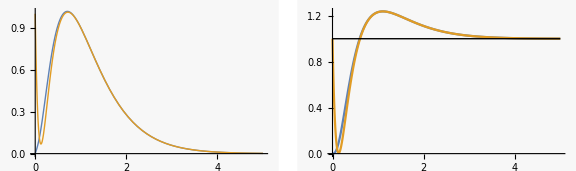

```mathematica
tmax=5; x0 = {0,0,1,0};  (* initial state, vector inputs *)
uimp={0,DiracDelta[t]}; ustep={UnitStep[t],0};

G0=1/(1+s^2); G0tf=TransferFunctionModel[G0,s];
G0ss = StateSpaceModel[G0tf]; 
K = StateFeedbackGains[G0ss,{-2,-2}];   (* Feedback gains *)
L=EstimatorGains[G0ss,{-10,-10}] ;        (* Observer gains*)
{A,b,c,d}=Normal[G0ss];  (* get A, b, c matrices *)
A1 = A-b.K; A2 = A-b.K-L.c; Ac = ArrayFlatten[({{A, -b.K}, {L.c, A2}})]; (* for "big" system *)
kr = -1/(c.Inverse[A1].b);             (* feedforward gain *)
Bc = ArrayFlatten[({{b.kr}, {b.kr}})] (* command input *);

Bd=ArrayFlatten[({{b}, {{{0}, {0}}}})](* disturbance input *);
Bn =  ArrayFlatten[({{0}, {0}, {L}})](* measurement noise input *); 
Btot = ArrayFlatten[ ({{Bc, Bd}})]; Cc = ({{1, 0, 0, 0}, {0, 0, 1, 0}}); G1ss = StateSpaceModel[{Ac,Btot,Cc}];
y1 = OutputResponse[{G1ss,x0},uimp,{t,0,tmax}]  (* input disturbance *);

y2= OutputResponse[{G1ss,x0},ustep,{t,0,tmax}]  (* step command *);

p1=Plot[y1,{t,0,tmax},PlotRange->Full];
p2=Plot[{y2,1},{t,0,tmax},PlotRange->Full, PlotStyle->{,,{Black,Thin}}];
GraphicsRow[{p1,p2},ImageSize->Large]
```

```mathematica
Join[{G0,G0ss},MatrixForm /@ {K,L,kr}]
```

{1/(1+s^2),010-101100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic,(3 | 4),(20
99),(4)}

```mathematica
G1ss
```

010000-10-3-441200-20100990-103-440100000001000StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic2241FalseFalseFalseAutomaticNoneAutomatic

Export the data

```mathematica
dt=0.01;dat = Table[{y1[[1]],y1[[2]],y2[[1]],y2[[2]]},{t,0,tmax,dt}];
(* SetDirectory[NotebookDirectory[]] *)
(* Export["observerFeedback.dat", dat] *)
```

## Redo using built-in Mathematica commands

```mathematica
estreg=StateSpaceModel[EstimatorRegulator[G0ss,{L,K}],SystemsModelLabels->{{"y"},{"u"},{"x̂","x̂dot"}}]
```

-20120-103-499340yux̂x̂dotStateSpaceModelTrueTrueTrueFalse$CellContext`stname1$CellContext`stname2yux̂x̂dotIdentityAutomatic112111213132TrueTrueFalseAutomaticyux̂x̂dotAutomatic

```mathematica
closedLoop=StateSpaceModel[SystemsModelFeedbackConnect[G0ss,estreg],SystemsModelLabels->{{"u"},{"y"},{"x","xdot","x̂","x̂dot"}}]
```

01000-10-3-41200-2010990-103-4010000uyxxdotx̂x̂dotStateSpaceModelTrueTrueTrueFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4uyxxdotx̂x̂dotIdentityAutomatic1141112131323334TrueTrueFalseAutomaticuyxxdotx̂x̂dotAutomatic

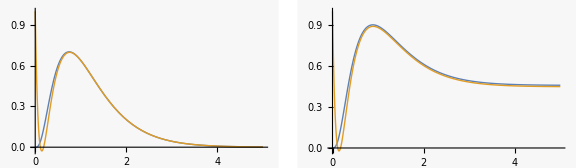

```mathematica
{xs1,xds1,xe1,xde1}=StateResponse[{closedLoop,x0},uimp,t];
{xs2,xds2,xe2,xde2}=StateResponse[{closedLoop,x0},ustep,t];
p1a=Plot[{xs1,xe1},{t,0,tmax},PlotRange->All];
p2a=Plot[{xs2,xe2},{t,0,tmax},PlotRange->All];
GraphicsRow[{p1a,p2a},ImageSize->Large]
```

```mathematica
(* the asymptotic step response is off because no ff is included... *)
```